## Unsupervised learning: Clustering

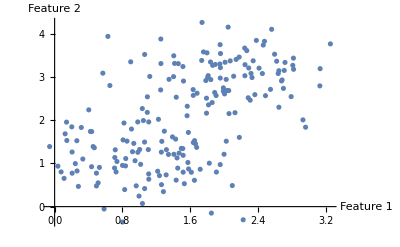
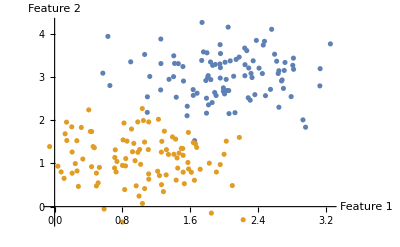
Given a set of data, the aim of data clustering is to identify groups (or clusters) of data, {G_1,G_2,...,G_K}, such that objects within a cluster are similar to other objects in the same cluster and are quite distinct to objects in different clusters. 

Data clustering is also called simply clustering, cluster analysis, segmentation analysis or taxonomy analysis.

Clustering differs from classification in the sense that the input data used for clustering are unlabelled, i.e. the aim is to infer classes instead of defining them using training data.

-Graphics-
Example: Given a data set with M=2 features, 

-Graphics-

We want to find the following clustering into two groups, G_1 and G_2, that are not known a priory:

-Graphics-

### Bibliography for clustering

Clustering is described in the books recommended at the beginning of the course and other books on machine learning.

There are also books with an exclusive focus on clustering. If you are interested, the following two are quite complete:

Gan, Guojun. et al. “Data clustering; theory, algorithms, and applications” SIAM (2007)

C. Aggarwal, C.K. Reddy “Data clustering algorithms and applications” Boca Raton, Fla. : CRC Press (2014). https://abdn.primo.exlibrisgroup.com/permalink/44ABE_INST/1jd70l9/alma9917747598305941

## Clustering methods

As shown in the diagram, clustering problems can be broadly divided in two categories:

Hard clustering: A data point belongs to one and only one cluster, G

Partitional: Create a non-overlapping partition of the data points.

Hierarchical: Define clusters sequentially. Impractical for large datasets.

Divisive: Start with a large cluster containing all the points in the data set and sequentially divide it into smaller clusters

Agglomerative: Start with clusters each containing one data point and proceeds by merging clusters

Fuzzy clustering: A data point may belong to two or more clusters with some probabilities.

The following table lists some of the most popular clustering methods (all available in Mathematica):

They can be implemented in Mathematica as follows:

FindClusters[data, Method → ”Method Name”]

## k Means clustering (KMC)

### Introduction

k means clustering (KMC) is the simplest and perhaps the most commonly used clustering method.

It is a partitional method.
 
Understanding the KMC clustering algorithm sets the basis to understand other clustering algorithms that were proposed after KMC.

Some ideas behind KMC are reminiscent of those for the kNN method for classification. However, KMC is unsupervised and KNN is supervised!

Central idea of KMC: Given a number of clusters, K, distribute a set of N points in clusters in such a way that 
	(i) differences within each cluster are minimised and
	(ii) differences between the clusters are maximised.

### The algorithm

#### Data

The algorithm is applied to a dataset consisting of N data points consisting of M features. 

Each point represents a feature vector with M components:

Point 1: x^(1)=(x_1^(1),x_2^(1),...,x_M^(1))
Point 2: x^(2)=(x_1^(2),x_2^(2),...,x_M^(2))
...
Point N: x^(N)=(x_1^(N),x_2^(N),...,x_M^(N))

Example: To illustrate the algorithm, we will consider a synthetic dataset with 

N = 200 points
M = 2 features

```mathematica
cluster1={{1.85715,2.41134},{2.68138,2.93472},{1.86266,3.27349},{1.78994,2.51212},{2.11024,3.02075},{1.80473,2.99734},{2.81659,3.18143},{2.06982,3.37715},{2.81486,3.44034},{2.34047,3.37884},{1.63287,2.7113},{1.09206,2.18332},{1.99996,2.64741},{2.24262,3.03314},{1.43366,2.53497},{1.90321,2.57411},{2.28785,3.21191},{2.36032,2.59448},{1.09353,2.54364},{1.98912,2.75204},{1.06139,3.52529},{1.73773,4.26741},{1.95077,3.75279},{0.568309,3.09197},{2.48553,2.57031},{2.54421,2.71681},{2.17502,3.4648},{0.896731,3.35464},{2.30539,2.46603},{3.12653,2.79729},{2.0299,2.68885},{1.25182,3.8836},{2.12625,2.17631},{2.40963,3.20857},{2.80744,3.27316},{2.71558,3.3407},{1.7961,3.56342},{1.41383,3.3181},{1.64971,1.5287},{2.59288,3.53098},{2.70657,3.1556},{0.627681,3.94391},{1.81038,3.03446},{1.40194,3.01153},{1.24978,2.70373},{2.95809,1.83996},{2.64347,2.30313},{1.9888,2.67487},{3.12969,3.19631},{1.73359,3.38654},{1.81393,2.358},{2.02228,2.94793},{1.51906,2.90944},{2.67489,2.91139},{2.26504,3.61469},{2.00922,3.34502},{1.9523,2.97885},{2.63549,3.08411},{2.05554,2.15475},{2.3267,2.99123},{1.56118,2.10632},{1.89394,3.29367},{2.28193,2.52173},{1.79033,2.16547},{2.44881,3.08366},{2.92723,2.00971},{2.24054,3.67338},{2.31506,3.08659},{1.40406,3.49446},{1.84084,2.94288},{1.75467,3.58422},{2.64329,3.14891},{2.45944,3.74346},{3.2505,3.77074},{0.651407,2.80561},{2.78805,2.54861},{1.45781,3.31294},{1.94777,3.30447},{2.24405,3.28837},{1.12145,3.01562},{1.95385,3.21985},{2.05217,2.68925},{1.25297,3.31439},{2.04531,4.15882},{1.95514,3.54649},{2.37795,3.85129},{1.5634,2.32555},{1.83748,3.3511},{2.69711,2.73896},{2.4736,3.83076},{1.34842,2.94941},{2.00323,2.6118},{1.63437,2.57731},{1.67919,2.62725},{2.13931,3.41066},{1.51253,3.2455},{2.61729,3.36875},{1.78227,2.92131},{1.88684,2.64426},{2.55805,4.10845}};
cluster2={{1.46736,1.2404},{1.00218,1.32401},{1.5287,0.531519},{0.314438,1.83405},{1.71592,0.865923},{0.143828,1.53209},{1.84762,-0.149994},{1.65977,1.45681},{1.10435,1.32171},{0.800759,-0.356508},{1.42653,1.56468},{0.980027,1.96224},{1.21476,0.819688},{1.01358,0.979574},{0.264413,0.826705},{1.64797,0.610394},{0.279895,0.468576},{1.67428,1.37275},{2.17725,1.60418},{1.49355,1.34929},{1.31789,1.32},{0.332393,1.10268},{1.10933,1.96241},{2.02341,1.51622},{1.95194,0.974225},{0.709479,1.13867},{1.57904,0.873125},{1.51511,0.798563},{1.99743,1.21331},{-0.0590018,1.39163},{1.57104,1.02261},{0.243771,0.996689},{0.202111,1.84829},{1.90692,0.80077},{1.51044,1.34561},{1.29328,1.74776},{1.28252,0.347363},{2.09426,0.487987},{1.82321,1.00662},{0.513042,0.550535},{1.10855,0.758026},{1.61153,0.796638},{2.22274,-0.304812},{0.825762,0.395356},{0.123747,1.68672},{0.800166,0.955164},{0.492922,0.479577},{1.38905,1.61546},{0.402461,2.24191},{1.0604,1.49586},{0.0766019,0.803721},{0.853009,1.5174},{0.724777,0.80391},{0.714742,1.31636},{0.80697,1.54542},{0.492863,0.776284},{0.917993,1.27217},{1.4059,1.2127},{0.905937,1.79774},{1.51479,1.18871},{0.994909,0.243867},{0.583107,-0.0545616},{0.454083,1.39121},{0.262081,1.52714},{1.03517,0.0719902},{1.22379,2.02375},{0.981142,1.25926},{0.817553,1.93696},{0.961803,0.481875},{0.111406,0.654609},{0.706548,0.894015},{0.948125,1.06342},{0.835697,0.942917},{0.436464,1.73916},{1.45104,0.892749},{1.63507,1.48438},{0.932851,1.46503},{0.421957,1.74105},{1.10994,0.635651},{0.838398,1.11351},{0.140319,1.95747},{0.206865,0.77477},{1.57639,1.71877},{1.3146,0.735394},{0.527658,0.908751},{1.34177,1.20899},{1.2598,0.50901},{0.435687,0.924509},{0.205958,1.2652},{1.04657,1.99471},{0.468013,1.36422},{1.26345,1.51241},{0.0386542,0.936882},{1.23598,0.718665},{1.25793,1.26298},{1.06108,0.418207},{1.03342,2.27221},{1.44321,1.12878},{1.43248,0.614069},{0.734678,1.04533}};

data=Join[cluster1,cluster2];
ListPlot[data,AxesLabel->{"Feature 1","Feature 2"}]
```

-Graphics-

```mathematica
cluster1//Length
```

100

In fact, the data consists of two clusters:

```mathematica
ListPlot[{cluster1,cluster2},AxesLabel->{"Feature 1","Feature 2"}]
```

-Graphics-

But we will pretend that we don’t know that the data consists of two clusters.

Aim: Find the clusters!

The KMC method basically consists in four steps that are iterated until it converges to a set of K clusters (the number of clusters is set by us) .

#### Step 1 - Pick K centres

We first decide on the number of clusters K. 

We then pick K centres, one  for each cluster. The idea is that each centre will represent a cluster. 

The centres are given by a set of M features, as the data vectors:

Centre 1: c^(1)=(c_1^(1),c_2^(1),...,c_M^(1))
Centre 2: c^(2)=(c_1^(2),c_2^(2),...,c_M^(2))
...
Centre K: c^(K)=(c_1^(K),c_2^(K),...,c_M^(K))

The centres can be drawn at random or taken as K random points from the dataset {x^(1),x^(2),...,x^(N)}

Example: Take K = 2 of the points in the dataset at random:

```mathematica
c=RandomSample[data,2]
```

{{1.25182,3.8836},{0.568309,3.09197}}

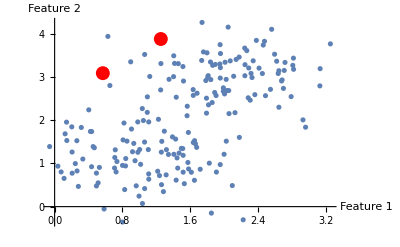

```mathematica
Show[ListPlot[data,AxesLabel->{"Feature 1","Feature 2"}],ListPlot[c,PlotStyle->{Red,PointSize[0.025]}]]
```

#### Step 2 - Find distances of each data point to the centres

Several definitions can be used for distance (several will be introduced in a section below). The specific choice depends on the problem at hand. 

Here, I will use the Euclidean distance. The Euclidean distance between the n-th datum, x^(n), and the k-th centre is, c^(k), is given by

d(x^(n),c^(k))=√((x_1^(n)-c_1^(k))^2+(x_2^(n)-c_2^(k))^2+⋯+(x_M^(n)-c_M^(k))^2)=√(∑_(m=1)^M (x_m^(n)-c_m^(k))^2)

The Euclidean distance can be easily calculated in Mathematica with the function EuclideanDistance

Example: For our synthetic data, the distance to the centres is

```mathematica
dToCentres=Table[{EuclideanDistance[data[[i]],c[[1]]],EuclideanDistance[data[[i]],c[[2]]]},{i,1,Length[data]}];
```

```mathematica
dToCentres
```

{{0.663372,1.53408},{0.661151,2.45493},{0.278289,2.30847},{0.590764,1.58625},{0.0853716,2.18656},{0.232346,2.03062},{0.796592,2.72909},{0.327876,2.48504},{0.875268,2.92834},{0.450624,2.61179},{0.523493,1.70125},{1.27863,1.06334},{0.405375,1.80989},{0.212778,2.26559},{0.789507,1.47061},{0.494224,1.69656},{0.303061,2.44136},{0.563617,1.9872},{1.06594,1.4232},{0.302447,1.89337},{1.0788,2.40351},{1.25058,3.22492},{0.705703,2.78861},{1.46289,2.02235},{0.662255,2.05627},{0.613064,2.202},{0.437675,2.60944},{1.1737,2.23632},{0.64684,1.85569},{1.12501,2.6869},{0.362773,1.86093},{1.13963,2.77079},{0.880518,1.52395},{0.410197,2.5037},{0.807767,2.79311},{0.743438,2.78886},{0.562982,2.56001},{0.671917,2.23007},{1.56984,0.744723},{0.738844,2.87379},{0.683875,2.63823},{1.66267,2.84981},{0.220933,2.06709},{0.629983,1.92656},{0.854857,1.59746},{1.52587,2.06133},{0.967364,2.00294},{0.379069,1.82718},{1.10853,2.95446},{0.447674,2.37252},{0.726689,1.46585},{0.104029,2.08009},{0.530976,1.8542},{0.65933,2.43335},{0.609906,2.78369},{0.294179,2.43078},{0.106929,2.07511},{0.605716,2.53786},{0.897218,1.45836},{0.302151,2.27731},{1.05546,1.12045},{0.277985,2.33871},{0.586455,1.88067},{0.91816,1.29353},{0.41939,2.42339},{1.37457,2.09841},{0.65623,2.82575},{0.286556,2.3498},{0.767278,2.40238},{0.218749,1.99492},{0.599853,2.56779},{0.620321,2.59314},{0.813943,2.98782},{1.41604,3.45902},{1.40101,1.72469},{0.909221,2.26728},{0.629625,2.23308},{0.266083,2.36917},{0.318733,2.48537},{0.909908,1.89599},{0.184928,2.29391},{0.363011,1.87337},{0.820869,2.20408},{1.10729,3.20334},{0.500595,2.59645},{0.871831,3.04582},{0.863423,1.31811},{0.356371,2.37223},{0.73616,2.32543},{0.89625,3.07135},{0.68984,1.85562},{0.440676,1.78177},{0.618067,1.57738},{0.551011,1.64089},{0.375121,2.54512},{0.553202,2.17852},{0.666874,2.75326},{0.280485,1.95181},{0.432,1.74886},{1.18112,3.35654},{1.89679,0.457132},{2.01057,0.203341},{2.56961,0.77564},{2.10425,1.00648},{2.20824,0.736101},{2.42261,0.972644},{3.20684,1.51441},{1.63737,0.716914},{1.9623,0.214553},{3.62325,1.49559},{1.60498,0.597073},{1.51346,0.84144},{2.37638,0.356541},{2.3082,0.142997},{2.84075,0.816676},{2.47104,0.805522},{3.12046,0.991676},{1.71628,0.69524},{1.45485,1.2483},{1.78505,0.520015},{1.87257,0.352836},{2.58504,0.693692},{1.42661,0.844503},{1.53542,1.07265},{2.07889,0.937848},{2.32484,0.316772},{2.22481,0.606647},{2.31129,0.586559},{1.83861,0.975892},{2.66875,1.11781},{2.08042,0.554218},{2.72317,0.792027},{2.18896,1.09814},{2.25425,0.937851},{1.78356,0.533706},{1.49792,0.680481},{2.80584,0.816108},{2.56442,1.24242},{2.0555,0.805706},{2.9255,0.767829},{2.47201,0.373305},{2.2936,0.67004},{3.36193,1.86241},{2.91676,0.753725},{2.34504,1.06423},{2.43089,0.280655},{2.99667,0.834711},{1.57296,0.612696},{1.81841,1.28166},{1.83351,0.375409},{2.97848,1.00117},{1.93408,0.431469},{2.59952,0.43799},{2.17778,0.366775},{1.94063,0.47659},{2.74626,0.635287},{2.09868,0.184831},{1.94215,0.390746},{1.6844,0.686245},{1.93302,0.493498},{2.9927,0.878724},{3.42692,1.25714},{2.28965,0.631923},{2.33492,0.864517},{3.14153,1.0501},{1.30673,0.923181},{2.07702,0.144302},{1.64744,0.841104},{2.78317,0.643364},{3.07069,1.02696},{2.5315,0.392339},{2.2638,0.0973286},{2.42375,0.261213},{2.06494,0.853325},{2.23532,0.483109},{1.61639,0.708856},{1.92936,0.355358},{2.07496,0.86476},{2.58546,0.493617},{2.27546,0.187611},{2.18415,1.21739},{2.91723,0.889539},{1.40813,0.811918},{2.42438,0.482594},{2.61742,0.5419},{1.96719,0.327699},{2.65689,0.656173},{2.65867,0.622312},{2.55358,0.832261},{1.44412,0.87291},{2.29981,0.608104},{1.71982,0.457005},{2.90519,1.00438},{2.46459,0.454848},{1.94842,0.27155},{2.80623,0.704723},{1.26568,1.15019},{2.01057,0.417449},{2.50987,0.650706},{2.38846,0.301075}}

#### Step 3 - Assign each point to the closest centre

In this step, we obtain K clusters, one associated to each centre

Example: For our example, the closest centre to a given point, data[[1]] say, can be calculated as follows:

```mathematica
dToCentres[[1]]
```

{0.663372,1.53408}

```mathematica
Min[dToCentres[[1]]]
```

0.663372

```mathematica
Position[dToCentres[[1]],Min[dToCentres[[1]]]]
```

{{1}}

Extending this to all points in the dataset, gives the following assignment of data points to the centres:

```mathematica
assigned=Flatten[Table[Position[dToCentres[[i]],Min[dToCentres[[i]]]],{i,1,Length[data]}]]
```

{1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

This defines K = 2 clusters in our example:

```mathematica
tempCluster1=data[[Flatten[Position[assigned,1]]]];
tempCluster2=data[[Flatten[Position[assigned,2]]]];
```

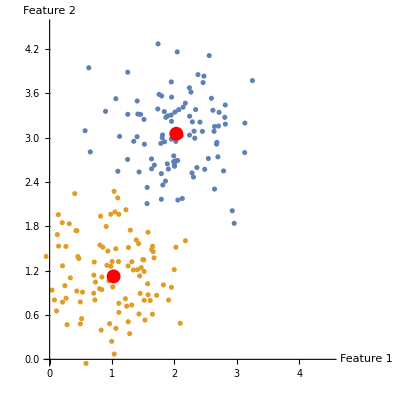

```mathematica
Show[ListPlot[{tempCluster1,tempCluster2},AxesLabel->{"Feature 1","Feature 2"},PlotRange->{{0,4.5},{0,4.5}},AspectRatio->1],ListPlot[c,PlotStyle->{Red,PointSize[0.025]}]]
```

#### Step 4 - Calculate new centres

New centres are given by the centroids of each of the clusters found in step 3. 

The centroid of the k-th centre is defined as the arithmetic mean of all the points in the cluster.

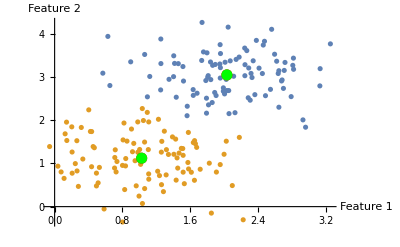

```mathematica
centreNew1={Mean[tempCluster1[[All,1]]],Mean[tempCluster1[[All,2]]]};
centreNew2={Mean[tempCluster2[[All,1]]],Mean[tempCluster2[[All,2]]]};
Show[ListPlot[{tempCluster1,tempCluster2},AxesLabel->{"Feature 1","Feature 2"}],ListPlot[c,PlotStyle->{Red,PointSize[0.02]}],ListPlot[{centreNew1,centreNew2},PlotStyle->{Green,PointSize[0.02]}],Graphics[Arrow[{c[[1]],centreNew1}]],Graphics[Arrow[{c[[2]],centreNew2}]]]
```

#### ***Iterate 2-4 until the centres do not change!!

Use the new centres obtained in 4 and repeat steps 2 to 4 until the centres do not change anymore. The clusters corresponding to the stable centres are the final result of the algorithm.

Example: Set c to the new centres and execute steps 2 to 4

```mathematica
c={centreNew1,centreNew2};
```

```mathematica
c
```

{{2.03065,3.05162},{1.02581,1.12205}}

### KMC using in Wolfram Language

The KMC method can be easily used in Mathematica using the FindClusters function

Example: When applied to the synthetic data, we obtain

```mathematica
clustersFC=FindClusters[data,2,Method->"KMeans",DistanceFunction->EuclideanDistance];
```

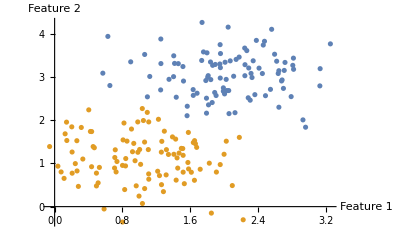

```mathematica
ListPlot[clustersFC,AxesLabel->{"Feature 1","Feature 2"}]
```

```mathematica
Mean[clustersFC[[1]][[All,1]]]
```

2.03065

## Normalisation of the data

Since clustering methods use distance measures to quantify the similarity of data points, it is important to standardize data for clustering. This is done in the same way as explained before for the K Nearest Neighbours (KNN) classification method. FindClusters standardizes the data automatically.

## How to choose K for KMC?

In the example considered above, we set K = 2 because, in fact, we knew that the data consisted of two clusters. In general, however, we will not know a reasonable value of K. There are several ways to find a reasonable value of K. Here, we describe the scree plot which is typically effective and it is relatively easy to understand and implement.

### Scree plot

Adding up the squared distances of each point to the centre of the nearest cluster gives a measure of total distance within a cluster, dispersion or error.

Let G_k be the K-th cluster and c^(k) its centre. The error of points within G_k is given by the sum of the square the distance of each data point in G_k to the centre of the cluster:

Error^(k)=∑_(i∈G_k) d^2(x^(i),c^(k))

The total error is then the sum of errors for each cluster:

Error = ∑_(k=1)^K Error^(k)=Error^(1)+Error^(2)+...+Error^(K)

The error decays with the number of clusters, K. 

To see this, consider the extreme case with one cluster per point (i.e. K = N). In this case, the error is zero because the centre of each cluster coincides with the point!

The scree plot is the plot of the error vs. K

#### Example

Consider a synthetic dataset consisting of 5 clusters of M = 2 features:

```mathematica
a=1;
gaussian[μ_,σ_,n_]:=RandomVariate[MultinormalDistribution[μ,{{σ,0},{0,σ}}],n];
cluster1=gaussian[{0,0},0.1,50];
cluster2=gaussian[{a,a},0.1,50];
cluster3=gaussian[{a,-a},0.1,50];
cluster4=gaussian[{-a,-a},0.1,50];
cluster5=gaussian[{-a,a},0.1,50];

data=Join[cluster1,cluster2,cluster3,cluster4,cluster5];
```

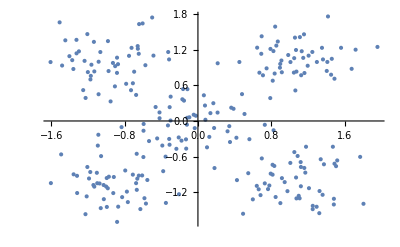

```mathematica
ListPlot[data]
```

```mathematica
PDF[MultinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{{σ,0},{0,σ}}],{x,y}]
```

(ⅇ^(1/2 (-(x-μ_1)^2/σ-(y-μ_2)^2/σ)))/(2 π √(σ^2))

```mathematica
Manipulate[Plot3D[PDF[MultinormalDistribution[{0,0},{{σ,0},{0,σ}}],{x,y}],{x,-5,5},{y,-5,5}],{σ,1,2}]
```

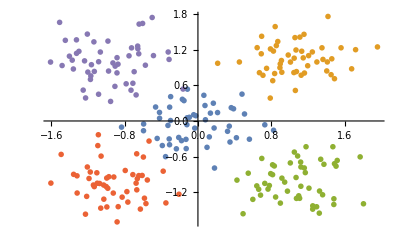

```mathematica
ListPlot[{cluster1,cluster2,cluster3,cluster4,cluster5},PlotStyle->PointSize[0.01]]
```

Let us find the clusters for a given K:

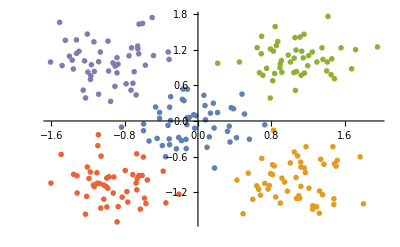

```mathematica
K=5;
clusters=FindClusters[data,K,Method->"KMeans",DistanceFunction->EuclideanDistance];
ListPlot[clusters,PlotStyle->PointSize[0.01]]
```

```mathematica
clusters[[1]]
```

{{0.561433,-0.30631},{-0.298917,0.0075587},{-0.0347617,-0.120624},{-0.0461928,0.105008},{0.363355,0.223409},{0.349751,-0.353921},{0.480853,0.451146},{0.419773,-0.281796},{0.124065,-0.267499},{-0.114588,0.534463},{0.508107,0.11761},{-0.23511,-0.46788},{-0.117732,0.0533263},{-0.152023,0.341681},{-0.327119,-0.0747502},{0.0817546,0.0204193},{-0.592395,-0.0504569},{-0.0936336,0.0618021},{-0.593694,-0.163838},{-0.419207,0.143879},{0.180822,-0.791182},{-0.313529,-0.301907},{-0.120504,-0.0624759},{-0.83326,-0.103616},{-0.297547,0.408843},{-0.0230003,0.0879644},{0.322985,-0.173635},{-0.309569,-0.399396},{0.0647098,0.431626},{-0.308459,0.232233},{0.214159,0.141122},{0.0991181,-0.442771},{0.729599,-0.0643604},{0.341981,-0.0872926},{-0.179056,-0.33073},{0.388392,0.204914},{-0.127921,-0.464456},{0.16813,0.298562},{-0.209702,-0.276988},{-0.169825,0.364499},{0.0769194,0.259879},{0.176479,-0.118112},{-0.353059,-0.599505},{-0.130382,-0.309024},{-0.444705,-0.293402},{0.136159,0.131767},{-0.418503,0.0457472},{-0.461734,0.234628},{-0.388566,-0.413024},{-0.533426,-0.337731},{-0.162078,0.536552}}

```mathematica
Mean[clusters[[1]]]
```

{-0.0592481,-0.043491}

In order to calculate the error of the clustering found above, we need to find the centre of each cluster first:

```mathematica
centres=Table[Mean[clusters[[i]]],{i,1,K}]
```

{{-0.0592481,-0.043491},{1.06545,-0.995728},{1.06988,1.04042},{-0.922204,-1.05127},{-0.979613,0.999424}}

```mathematica
centres[[1]]
```

{-0.0592481,-0.043491}

The error is

```mathematica
Table[EuclideanDistance[clusters[[1,j]],centres[[1]]],{j,1,Length[clusters[[1]]]}]
```

{0.674032,0.245045,0.0809266,0.149072,0.499829,0.513466,0.732377,0.535024,0.289453,0.580598,0.589785,0.459384,0.11311,0.396188,0.269688,0.15481,0.533192,0.110766,0.547829,0.405805,0.785286,0.362543,0.0641306,0.776343,0.511266,0.136361,0.403781,0.435119,0.491021,0.371658,0.329899,0.42954,0.789123,0.403613,0.311224,0.511944,0.42653,0.410733,0.277772,0.422709,0.332528,0.247256,0.628869,0.274896,0.459382,0.262487,0.370172,0.489229,0.494979,0.558052,0.589087}

Do the same for all the centres:

```mathematica
Table[Table[EuclideanDistance[clusters[[i,j]],centres[[i]]],{j,1,Length[clusters[[i]]]}],{i,1,Length[centres]}]
```

{{0.674032,0.245045,0.0809266,0.149072,0.499829,0.513466,0.732377,0.535024,0.289453,0.580598,0.589785,0.459384,0.11311,0.396188,0.269688,0.15481,0.533192,0.110766,0.547829,0.405805,0.785286,0.362543,0.0641306,0.776343,0.511266,0.136361,0.403781,0.435119,0.491021,0.371658,0.329899,0.42954,0.789123,0.403613,0.311224,0.511944,0.42653,0.410733,0.277772,0.422709,0.332528,0.247256,0.628869,0.274896,0.459382,0.262487,0.370172,0.489229,0.494979,0.558052,0.589087},{0.873059,0.639687,0.383115,0.340264,0.29329,0.356582,0.230042,0.197943,0.44639,0.469429,0.204195,0.839936,0.296296,0.803742,0.529805,0.123197,0.333623,0.521468,0.267711,0.226863,0.418984,0.045937,0.573986,0.15326,0.318247,0.116806,0.335914,0.299843,0.806196,0.430388,0.521108,0.457372,0.305757,0.309605,0.501613,0.507048,0.519747,0.566698,0.611154,0.165825,0.264224,0.500598,0.407875,0.694214,0.408936,0.562948,0.583427,0.36104,0.433957,0.472986,0.307322},{0.277554,0.911836,0.33663,0.326751,0.340733,0.464313,0.590868,0.228241,0.227359,0.857508,0.233072,0.443228,0.534022,0.0247799,0.628885,0.355782,0.713254,0.371357,0.160829,0.669122,0.0784816,0.108658,0.619692,0.389018,0.360711,0.152488,0.345269,0.796634,0.214568,0.148984,0.356788,0.311799,0.460154,0.52763,0.252081,0.210545,0.190281,0.465097,0.280411,0.535733,0.294295,0.169887,0.425027,0.526705,0.45198,0.145732,0.390397,0.390567,0.270438,0.0814912},{0.65907,0.28301,0.176305,0.397539,0.247786,0.214935,0.124794,0.259486,0.317846,0.150607,0.489478,0.109693,0.417425,0.273268,0.363038,0.436083,0.560496,0.581535,0.349679,0.279102,0.307552,0.0937977,0.520701,0.55231,0.737596,0.418968,0.682065,0.160743,0.254438,0.276376,0.200422,0.374955,0.659636,0.59865,0.646208,0.479746,0.460738,0.255217,0.83604,0.109615,0.247671,0.39264,0.100712,0.751255,0.400045,0.117371,0.219512,0.34193,0.426635},{0.665776,0.247015,0.371034,0.55996,0.361623,0.431932,0.364815,0.283966,0.454422,0.357978,0.190059,0.423162,0.34296,0.881933,0.552594,0.331513,0.7424,0.399618,0.413411,0.628455,0.543052,0.671389,0.501875,0.674341,0.411102,0.116532,0.214146,0.257468,0.224773,0.71387,0.639261,0.180433,0.358307,0.0575706,0.506799,0.103791,0.116633,0.660095,0.388755,0.343375,0.50426,0.392442,0.844418,0.109278,0.513446,0.160598,0.424462,0.306713,0.587317}}

The total error can be calculated as follows:

```mathematica
Total[Flatten[Table[Table[(EuclideanDistance[clusters[[i,j]],centres[[i]]])^2,{j,1,Length[clusters[[i]]]}],{i,1,Length[centres]}]]]
```

49.3847

#### A function for the scree plot

We can put together the instructions used above to define a function to calculate the error for any value of K

```mathematica
errorKMC[data_,k_]:=Module[{data0=data,nc=k,clusters,centre},
clusters=FindClusters[data0,nc,Method->"KMeans"];
centre=Table[Mean[clusters[[i]]],{i,1,nc}];
Total[Flatten[Table[Table[(EuclideanDistance[clusters[[i,j]],centre[[i]]])^2,{j,1,Length[clusters[[i]]]}],{i,1,Length[centre]}]]]]
```

```mathematica
errorKMC[data,5]
```

49.3873

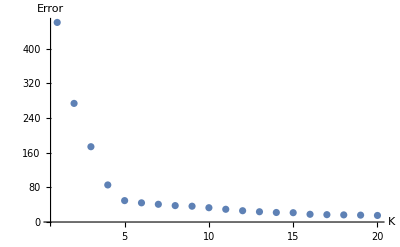

```mathematica
scree=Table[{k,errorKMC[data,k]},{k,1,20}];
ListPlot[scree,PlotRange->All,AxesLabel->{"K","Error"}]
```

The plot exhibits a shoulder for K = 5: The error decreases faster for K < 5 than for K > 5. 

This can be seen in the plot of the differences between consecutive errors:

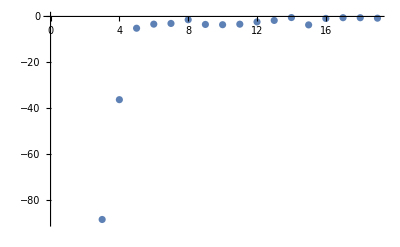

```mathematica
ListPlot[Differences[scree][[All,2]]]
```

Conclusion: The appearance of a clear shoulder in the scree plot indicates an optimal value K* of the number of clusters.

## Distance functions

One can use several measures for the distance between two vectors u=(u_1,u_2,... u_M) and v=(v_1,v_2,... v_M)

Some of the most widely used distances follow:

### Euclidean norm

EuclideanDistance[u,v]=√(∑_(i=1)^M (u_i-v_i)^2)

It is the most widely used distance. It is used by default when dealing with numerical data.

Example: The Euclidean distance between the points (1,2) and (3,3) is

```mathematica
EuclideanDistance[{{1,2}},{{3,3}}]
```

√5

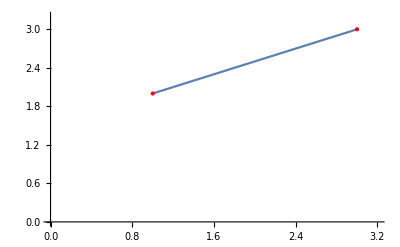

```mathematica
Show[ListPlot[{{1,2},{3,3}},Joined->True,PlotRange->{{0,3.2},{0,3.2}}],ListPlot[{{1,2},{3,3}},PlotStyle->{Red,PointSize[Large]}]]
```

### Manhattan distance

ManhattanDistance[u,v]=∑_(i=1)^M |u_i-v_i|=|u_1-v_1|+|u_2-v_2|

It is sometimes preferable to the Euclidean norm when dealing with high dimensional data

Example:

```mathematica
ManhattanDistance[{1,2},{3,3}]
```

3

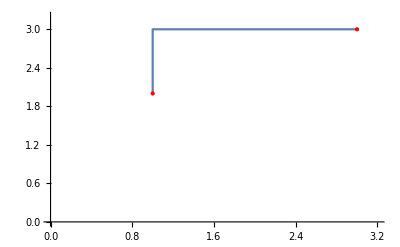

```mathematica
Show[ListPlot[{{1,2},{1,3},{2,3},{3,3}},InterpolationOrder->0,Joined->True,PlotRange->{{0,3.2},{0,3.2}}],ListPlot[{{1,2},{3,3}},PlotStyle->{Red,PointSize[Large]}]]
```

### Chessboard or Chebyshev distance

ChessboardDistance[u,v]=max_i [|u_i-v_i|]

This can be the preferred distance measure when data has many dimensions and most of them do not play an important role for classification or clustering

Example:

```mathematica
ChessboardDistance[{1,2},{3,3}]
```

2

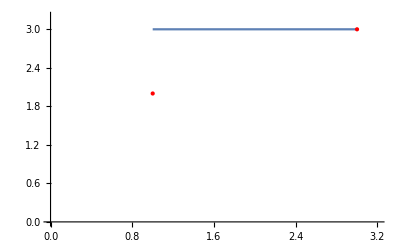

```mathematica
Show[ListPlot[{{1,3},{3,3}},Joined->True,PlotRange->{{0,3.2},{0,3.2}}],ListPlot[{{1,2},{3,3}},PlotStyle->{Red,PointSize[Large]}]]
```

### Cosine distance

CosineDistance[u,v]=1-Cos[OverHat[uv]]=1-(u.v)/(|u||v|)

Here, OverHat[uv] is the angle between vector u and v

The cosine distance is appropriate when two vectors are similar if they are pointing in the same direction even if they are of different lengths.

Example:

```mathematica
CosineDistance[{1,2},{3,3}]
```

1-3/(√10)

```mathematica
%//N
```

0.0513167

```mathematica
Show[ListPlot[{{1,2},{3,3}},PlotStyle->{Red,PointSize[Large]},PlotRange->{{0,3.2},{0,3.2}}],Graphics[Arrow[{{0,0},{1,2}}]],Graphics[Arrow[{{0,0},{3,3}}]]]
```

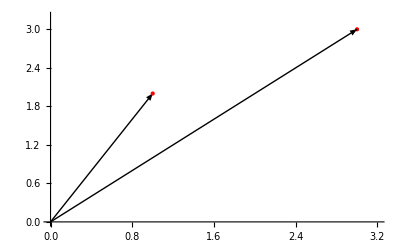

### A case where cosine distance is appropriate

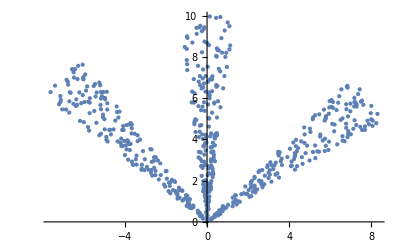

```mathematica
p1=Table[RandomReal[{0,10}] {Cos[a=RandomReal[{π/6,π/4}]],Sin[a]},{200}];
p2=Table[RandomReal[{0,10}] {Cos[a=RandomReal[{(11 π)/24,(13 π)/24}]],Sin[a]},{200}];
p3=Table[RandomReal[{0,10}] {Cos[a=RandomReal[{(17 π)/24,(19 π)/24}]],Sin[a]},{200}];
data=Join[p1,p2,p3];
ListPlot[data,PlotStyle->PointSize[Medium]]
```

Humans can identify three clusters. However, applying the FindClusters blindly do not find the clustering we expect.

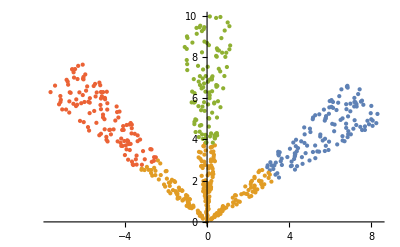

```mathematica
ListPlot[FindClusters[data],PlotStyle->PointSize[Medium]]
```

It finds 4 clusters,

```mathematica
Length[FindClusters[data]]
```

4

Specifying that we want to cluster the data in 3 groups and Euclidean distance function does not work as we expect either:

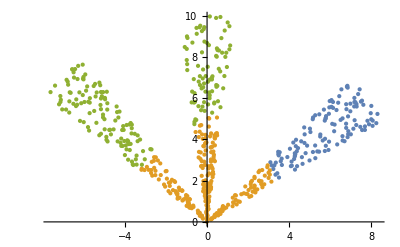

```mathematica
ListPlot[FindClusters[data,3,Method->"KMeans",DistanceFunction->EuclideanDistance],PlotStyle->PointSize[Medium]]
```

In contrast, using the cosine distance gives the clustering we expect:

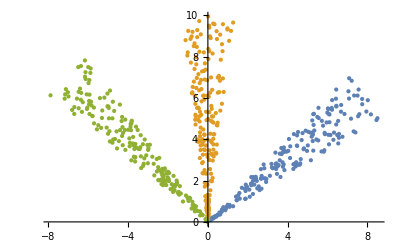

```mathematica
ListPlot[FindClusters[data,DistanceFunction->CosineDistance],PlotStyle->PointSize[Medium]]
```

However, it does not work so well for our original dataset:

```mathematica
a=1;
gaussian[μ_,σ_,n_]:=RandomVariate[MultinormalDistribution[μ,{{σ,0},{0,σ}}],n];
cluster1=gaussian[{0,0},0.1,50];
cluster2=gaussian[{a,a},0.1,50];
cluster3=gaussian[{a,-a},0.1,50];
cluster4=gaussian[{-a,-a},0.1,50];
cluster5=gaussian[{-a,a},0.1,50];

data=Join[cluster1,cluster2,cluster3,cluster4,cluster5];
```

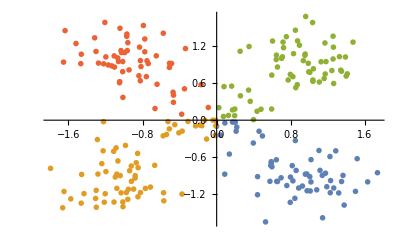

```mathematica
K=4;
clusters=FindClusters[data,K,Method->"KMeans",DistanceFunction->CosineDistance];
ListPlot[clusters,PlotStyle->PointSize[0.01]]
```

## Other clustering algorithms

### Agglomerative method

Start with clusters each containing one data point and proceeds by merging clusters.

#### Simple dataset

Let us explore an agglomerative method applied to a very simple dataset:

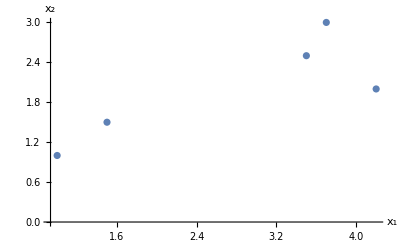

```mathematica
data={{1,1},{1.5,1.5},{3.5,2.5},{3.7,3},{4.2,2}};
ListPlot[data,AxesLabel->{"x_1","x_2"}]
```

The nearest neighbours can be visually identified for this simple dataset.

The values of distances between all pairs of points can be explored with DistanceMatrix:

```mathematica
distM=DistanceMatrix[data];
MatrixForm[distM]
```

(0. | 0.707107 | 2.91548 | 3.36006 | 3.35261
0.707107 | 0. | 2.23607 | 2.66271 | 2.74591
2.91548 | 2.23607 | 0. | 0.538516 | 0.860233
3.36006 | 2.66271 | 0.538516 | 0. | 1.11803
3.35261 | 2.74591 | 0.860233 | 1.11803 | 0.)

Dendrogram function constructs a dendrogram from the hierarchical clustering of the data points:

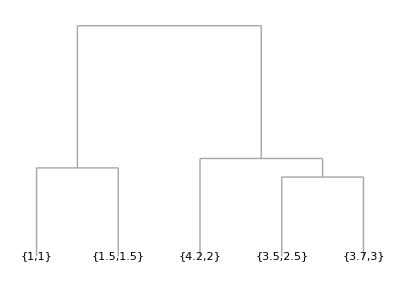

```mathematica
Dendrogram[data]
```

The proximity between points can be visualised using NearestNeighborGraph:

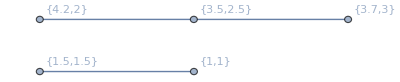

```mathematica
NearestNeighborGraph[data,VertexLabels->All]
```

One can also use FindClusters to find and agglomerate clustering which corresponds to some level in the dendrogram that gives a reasonable clustering (i.e. small distance within clusters and large distance between clusters)

```mathematica
FindClusters[data,Method->"Agglomerate"]
```

{{{1,1},{1.5,1.5}},{{3.5,2.5},{3.7,3},{4.2,2}}}

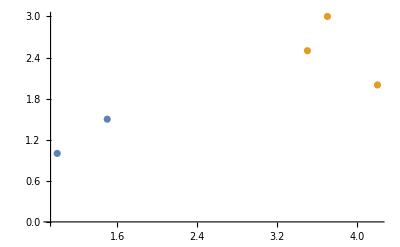

```mathematica
ListPlot[%]
```

#### Other type of data

Dendrogram can be applied to many types of data

For example:

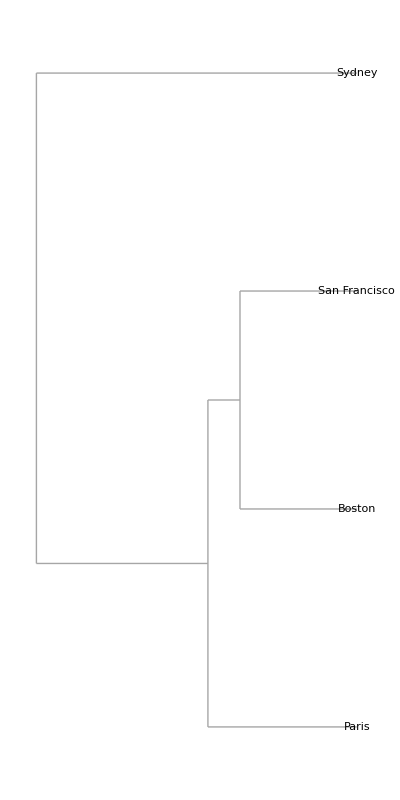

```mathematica
Dendrogram[{Entity["City",{"Paris","IleDeFrance","France"}],Entity["City",{"Sydney","NewSouthWales","Australia"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"SanFrancisco","California","UnitedStates"}]}, Left]
```

Although it is not specified in the above example, it uses the coordinates of cities to measure distances. 

This can be seen by realising that the dendrogram obtained by explicitly using coordinates has the same topology as the one used without specifying the coordinates.

```mathematica
Entity["City",{"Paris","IleDeFrance","France"}]["Population"]
```

2206488 people

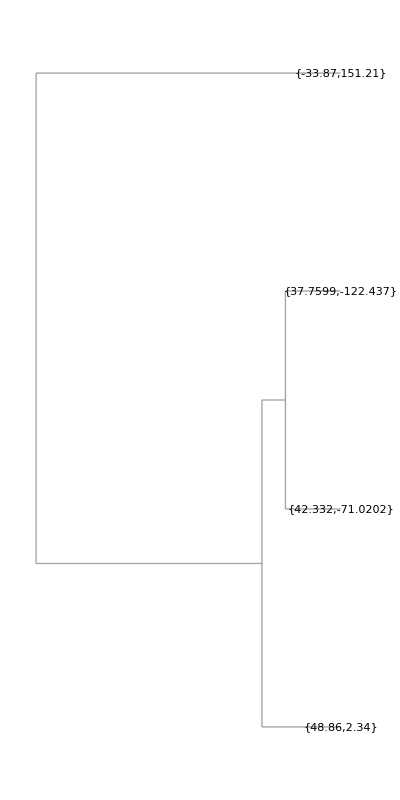

```mathematica
Dendrogram[{Entity["City",{"Paris","IleDeFrance","France"}]["Coordinates"],Entity["City",{"Sydney","NewSouthWales","Australia"}]["Coordinates"],Entity["City",{"Boston","Massachusetts","UnitedStates"}]["Coordinates"],Entity["City",{"SanFrancisco","California","UnitedStates"}]["Coordinates"]}, Left]
```

### DBSCAN (Density-based scanning of the feature space)

DBSCAN is perhaps the most popular density-based clustering method.

The main idea of the algorithm is that a point in the dataset belongs to a cluster if it is close to many points from that cluster.

DBSCAN uses two parameters:

r  (NeighborhoodRadius in Mathematica): Radius of a neighbourhood with respect to any data point.

N_min (NeighborsNumber in Mathematica): Minimum number of points in the neighbourhood of radius r for a point to be considered to belong to a cluster.

Brief description of the algorithm (not essential for the course):

Starts from an arbitrary point P in the dataset that has not been visited before.

Check the number of points N in the neighbourhood of radius r of point P.

If the neighbourhood contains a number of points N≥N_min, a cluster starts to grow. All the points in the neighbourhood of P are assigned to the growing cluster. If the newly assigned points have N≥N_min points in their r-neighbourhood, they are also included in the growing cluster. Growth stops when all newly included points have N<N_min in their r-neighbourhood.

If the r-neighbourhood of P contains N<N_min points, the point P is classified as noise for the moment (it might become part of a cluster at later stages of the algorithm).

Return to step 1 while there are points not visited by the algorithm.

Let us consider the following dataset:

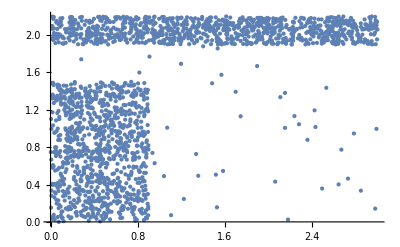

```mathematica
SeedRandom[2]
Dis=MixtureDistribution[{2,2,0.1},{UniformDistribution[{{-0,0.9}, {0,1.5}}],
UniformDistribution[{{0,3},{ 1.9,2.2}}],UniformDistribution[{{0,3},{ 0,2.2}}]}];
data=RandomVariate[Dis,2000];
ListPlot[data, PlotRange->All,PlotStyle->PointSize[Medium]]
```

Let us compare KMC and DBSCAN

Clustering the data in 2 clusters by using the KMC method:

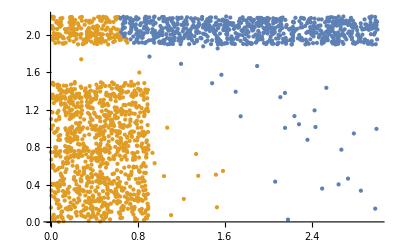

```mathematica
ListPlot[FindClusters[data, 2, Method->"KMeans",DistanceFunction->ManhattanDistance],PlotStyle->PointSize[Medium]]
```

Note that using 3 clusters does not lead to something necessarily better.

DBSCAN does not necessarily do very well depending on the settings.

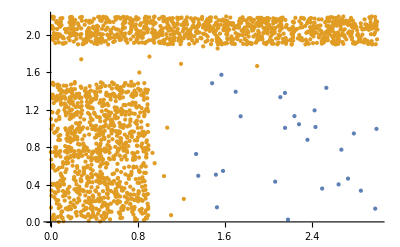

```mathematica
ListPlot[FindClusters[data, Method->"DBSCAN"],PlotStyle->PointSize[Medium]]
```

By default, DBSCAN predicts two clusters.

Tuning the neighborhood radius leads to a more meaningful clustering (from the human perspective...).

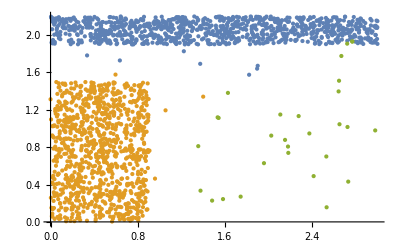

```mathematica
ListPlot[FindClusters[data, Method->{"DBSCAN","NeighborhoodRadius"->0.1}],PlotStyle->PointSize[Medium]]
```

```mathematica
Length[FindClusters[data, Method->{"DBSCAN","NeighborhoodRadius"->0.1}]]
```

3

The number of clusters predicted by DBSCAN normally depends on the radius r of the neighbourhood and number of neighbors required in the neighbourhood, N_min, to decide if a point belongs to a cluster or not. We can explore the number of clusters predicted by the DBSCAN method as a function of                                         r = NeighborhoodRadius. Three clusters (expected by humans) are found for a range of values of r.

```mathematica
NclusterVsRadius=Table[{r,
clusteringDBSCAN=FindClusters[data,Method->{"DBSCAN","NeighborhoodRadius"->r}];
Length[clusteringDBSCAN]},{r,0.05,1,0.02}];
```

```mathematica
NclusterVsRadius
```

{{0.05,84},{0.07,7},{0.09,3},{0.11,3},{0.13,3},{0.15,3},{0.17,3},{0.19,3},{0.21,3},{0.23,3},{0.25,3},{0.27,2},{0.29,2},{0.31,2},{0.33,2},{0.35,2},{0.37,2},{0.39,2},{0.41,2},{0.43,2},{0.45,2},{0.47,2},{0.49,2},{0.51,2},{0.53,2},{0.55,2},{0.57,2},{0.59,2},{0.61,1},{0.63,1},{0.65,1},{0.67,1},{0.69,1},{0.71,1},{0.73,1},{0.75,1},{0.77,1},{0.79,1},{0.81,1},{0.83,1},{0.85,1},{0.87,1},{0.89,1},{0.91,1},{0.93,1},{0.95,1},{0.97,1},{0.99,1}}

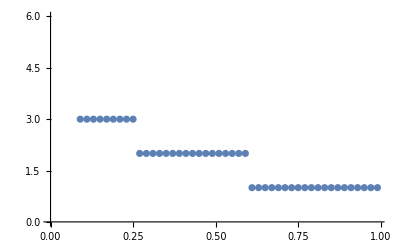

```mathematica
ListPlot[NclusterVsRadius]
```

One would intuitively expect the following trends:

The number of clusters decreases with the neighbourhood radius r. Indeed, the larger the radius, the higher the chances for a point to be “invaded” by a growing cluster. Think about the limit with r→ ∞.

The number of clusters increases with the minimal number of points N_min in the r-neighbourhood. Indeed, if one requires a large number of points in the r-neighbourhood for the cluster to grow, it is unlikely that clusters will grow much.

For a 2-dimensional dataset, one can explore the effect of r and N_min visually:

```mathematica
Manipulate[TableForm[{ListPlot[FindClusters[data, Method->{"DBSCAN","NeighborhoodRadius"->r,"NeighborsNumber"->Nmin}],PlotStyle->PointSize[Medium]],{"Number of clusters: "<>ToString[Length[FindClusters[data, Method->{"DBSCAN","NeighborhoodRadius"->r,"NeighborsNumber"->Nmin}]]]}}],{r,0.05,0.5},{Nmin,1,50,5}]
```

FindClusters::mlmpty: The dataset should contain at least one example.

General::stop: Further output of FindClusters::mlmpty will be suppressed during this calculation.

ListPlot::lpn: FindClusters[data,Method→{DBSCAN,NeighborhoodRadius→0.12,NeighborsNumber→10.}] is not a list of numbers or pairs of numbers.

FindClusters::mlmpty: The dataset should contain at least one example.

General::stop: Further output of FindClusters::mlmpty will be suppressed during this calculation.

FindClusters::numclus: The number of clusters False can only be either a positive integer or Automatic.

ListPlot::lpn: FindClusters[data,Method→{DBSCAN,NeighborhoodRadius→0.12,NeighborsNumber→10.}] is not a list of numbers or pairs of numbers.

For r=0.12 it looks like one gets three reasonable clusters which do not depend much on N_min (but, of course, if N_min is large enough (e.g. N_min larger than 20) the number of clusters is larger than three.

## Building a classifier in an unsupervised way

For classification, we use data from known classes. Classes are normally defined by humans (e.g. species of iris flowers, the type of animal, etc). Is in this sense that classification is a supervised machine learning task (humans are supervising...).

Given a dataset, however, one could do classification in a completely unsupervised way by
(i) Find clusters in the data
(ii) Define a class based on each cluster. 
(iii) Train a classifier using the data labeled by the clusters.

### ClusterClassify function

In Mathematica, this can be achieved with the ClusterClassify function which generates a ClassifierFunction[…] by partitioning data into clusters of similar elements.

Let us consider the data set used at the beginning of this section.

```mathematica
data=Join[cluster1,cluster2];
```

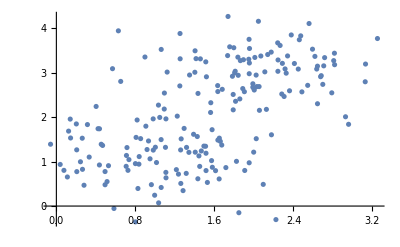

```mathematica
ListPlot[data]
```

The data consists of two clusters but we will pretend that this is unknown to us for the moment.

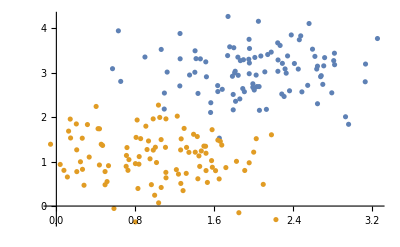

```mathematica
ListPlot[{cluster1,cluster2}]
```

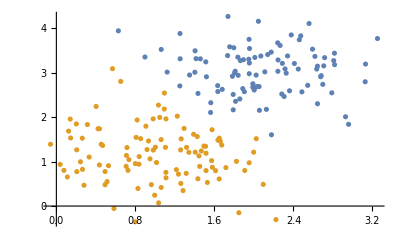

```mathematica
ListPlot[FindClusters[data,2,Method->"KMeans"]]
```

```mathematica
FindClusters[data,2,Method->"KMeans"]
```

{{{1.85715,2.41134},{2.68138,2.93472},{1.86266,3.27349},{1.78994,2.51212},{2.11024,3.02075},{1.80473,2.99734},{2.81659,3.18143},{2.06982,3.37715},{2.81486,3.44034},{2.34047,3.37884},{1.63287,2.7113},{1.99996,2.64741},{2.24262,3.03314},{1.43366,2.53497},{1.90321,2.57411},{2.28785,3.21191},{2.36032,2.59448},{1.98912,2.75204},{1.06139,3.52529},{1.73773,4.26741},{1.95077,3.75279},{2.48553,2.57031},{2.54421,2.71681},{2.17502,3.4648},{0.896731,3.35464},{2.30539,2.46603},{3.12653,2.79729},{2.0299,2.68885},{1.25182,3.8836},{2.12625,2.17631},{2.40963,3.20857},{2.80744,3.27316},{2.71558,3.3407},{1.7961,3.56342},{1.41383,3.3181},{2.59288,3.53098},{2.70657,3.1556},{0.627681,3.94391},{1.81038,3.03446},{1.40194,3.01153},{1.24978,2.70373},{2.95809,1.83996},{2.64347,2.30313},{1.9888,2.67487},{3.12969,3.19631},{1.73359,3.38654},{1.81393,2.358},{2.02228,2.94793},{1.51906,2.90944},{2.67489,2.91139},{2.26504,3.61469},{2.00922,3.34502},{1.9523,2.97885},{2.63549,3.08411},{2.05554,2.15475},{2.3267,2.99123},{1.56118,2.10632},{1.89394,3.29367},{2.28193,2.52173},{1.79033,2.16547},{2.44881,3.08366},{2.92723,2.00971},{2.24054,3.67338},{2.31506,3.08659},{1.40406,3.49446},{1.84084,2.94288},{1.75467,3.58422},{2.64329,3.14891},{2.45944,3.74346},{3.2505,3.77074},{2.78805,2.54861},{1.45781,3.31294},{1.94777,3.30447},{2.24405,3.28837},{1.12145,3.01562},{1.95385,3.21985},{2.05217,2.68925},{1.25297,3.31439},{2.04531,4.15882},{1.95514,3.54649},{2.37795,3.85129},{1.5634,2.32555},{1.83748,3.3511},{2.69711,2.73896},{2.4736,3.83076},{1.34842,2.94941},{2.00323,2.6118},{1.63437,2.57731},{1.67919,2.62725},{2.13931,3.41066},{1.51253,3.2455},{2.61729,3.36875},{1.78227,2.92131},{1.88684,2.64426},{2.55805,4.10845},{2.17725,1.60418}},{{1.09206,2.18332},{1.09353,2.54364},{0.568309,3.09197},{1.64971,1.5287},{0.651407,2.80561},{1.46736,1.2404},{1.00218,1.32401},{1.5287,0.531519},{0.314438,1.83405},{1.71592,0.865923},{0.143828,1.53209},{1.84762,-0.149994},{1.65977,1.45681},{1.10435,1.32171},{0.800759,-0.356508},{1.42653,1.56468},{0.980027,1.96224},{1.21476,0.819688},{1.01358,0.979574},{0.264413,0.826705},{1.64797,0.610394},{0.279895,0.468576},{1.67428,1.37275},{1.49355,1.34929},{1.31789,1.32},{0.332393,1.10268},{1.10933,1.96241},{2.02341,1.51622},{1.95194,0.974225},{0.709479,1.13867},{1.57904,0.873125},{1.51511,0.798563},{1.99743,1.21331},{-0.0590018,1.39163},{1.57104,1.02261},{0.243771,0.996689},{0.202111,1.84829},{1.90692,0.80077},{1.51044,1.34561},{1.29328,1.74776},{1.28252,0.347363},{2.09426,0.487987},{1.82321,1.00662},{0.513042,0.550535},{1.10855,0.758026},{1.61153,0.796638},{2.22274,-0.304812},{0.825762,0.395356},{0.123747,1.68672},{0.800166,0.955164},{0.492922,0.479577},{1.38905,1.61546},{0.402461,2.24191},{1.0604,1.49586},{0.0766019,0.803721},{0.853009,1.5174},{0.724777,0.80391},{0.714742,1.31636},{0.80697,1.54542},{0.492863,0.776284},{0.917993,1.27217},{1.4059,1.2127},{0.905937,1.79774},{1.51479,1.18871},{0.994909,0.243867},{0.583107,-0.0545616},{0.454083,1.39121},{0.262081,1.52714},{1.03517,0.0719902},{1.22379,2.02375},{0.981142,1.25926},{0.817553,1.93696},{0.961803,0.481875},{0.111406,0.654609},{0.706548,0.894015},{0.948125,1.06342},{0.835697,0.942917},{0.436464,1.73916},{1.45104,0.892749},{1.63507,1.48438},{0.932851,1.46503},{0.421957,1.74105},{1.10994,0.635651},{0.838398,1.11351},{0.140319,1.95747},{0.206865,0.77477},{1.57639,1.71877},{1.3146,0.735394},{0.527658,0.908751},{1.34177,1.20899},{1.2598,0.50901},{0.435687,0.924509},{0.205958,1.2652},{1.04657,1.99471},{0.468013,1.36422},{1.26345,1.51241},{0.0386542,0.936882},{1.23598,0.718665},{1.25793,1.26298},{1.06108,0.418207},{1.03342,2.27221},{1.44321,1.12878},{1.43248,0.614069},{0.734678,1.04533}}}

To assign data points to classes, we use the ClusterClassify function:

```mathematica
cc=ClusterClassify[data,2,Method->"KMeans"]
```

ClassifierFunction[…]

For this dataset, ClusterClassify finds a partition of two classes and assigns each point to one class.

Points in cluster1 are mostly assigned to class 2:

```mathematica
cc[cluster1]
```

{2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

1,2: Machine classification. cluster1, cluster2: Human classification.

Points in cluster2 are mostly assigned to class 1 :

```mathematica
cc[cluster2]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Of course, ClusterClassify does not know which data we defined as cluster 1 or cluster 2. This function just finds two classes which it calls 1 and 2 but the labels we gave as humans do not need to agree with the labels chosen by ClusterClassify.

Let us look at plots for the classification of what we called cluster1 and cluster2:

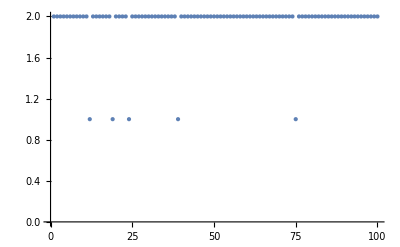

```mathematica
ListPlot[cc[cluster1],PlotStyle->PointSize[Medium]]
```

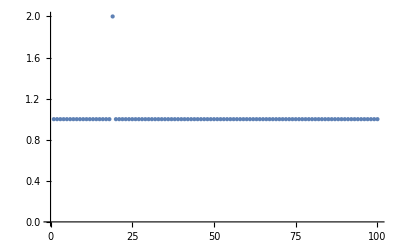

```mathematica
ListPlot[cc[cluster2],PlotStyle->PointSize[Medium]]
```

One can visualise the probability that any point in the space is assigned to a certain class.

For example, the probability that any point (x,y) is assigned to class 2 is

```mathematica
cc[{1,1},"Probabilities"]
```

<|1→0.999239,2→0.000761122|>

```mathematica
Plot3D[Values[cc[{x,y},"Probabilities"]][[2]],{x,0,5},{y,0,5},AxesLabel->{"x","y","P(class 2)"}]
```

-Graphics3D-

The probability changes when we go from one cluster to the other. Compare with this which can be regarded as a projection of the probability on the x-y plane:

```mathematica
ListPlot[FindClusters[data,2,Method->"KMeans"]]
```

-Graphics-

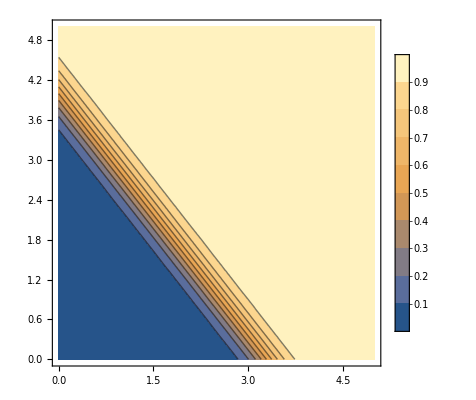

```mathematica
ContourPlot[Values[cc[{x,y},"Probabilities"]][[2]],{x,0,5},{y,0,5},PlotLegends->Automatic]
```

### How good is the classification?

If we take cluster1 and cluster2 as the true classification (e.g. true species determined by humans perhaps using more features), how good is unsupervised classification?

There are several measures to evaluate the results.

#### Purity

Purity is perhaps the most basic measure to evaluate the “unsupervised” classifier. For each cluster, count the number of data points from the most common class in said cluster. Now take the sum over all clusters and divide by the total number of data points.

For the example studied above, one can proceed as follows:

The most common class in the true class cluster1 is

```mathematica
Commonest[cc[cluster1]]
```

{2}

```mathematica
cluster1//Length
```

100

```mathematica
cc[cluster2]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

The number of data points of the most common class in each true class is:

```mathematica
Count[cc[cluster1],Commonest[cc[cluster1]][[1]]]
```

95

```mathematica
Count[cc[cluster2],Commonest[cc[cluster2]][[1]]]
```

99

```mathematica
Length[data]
```

200

```mathematica
N[(95+99)/Length[data]]
```

0.97

One can define a modular function to automatically calculate the purity for any dataset, classifier and true classes:

```mathematica
Purity[datain_,classifierin_,trueclassesin_]:=Module[{data=datain,classifier=classifierin,trueclasses=trueclassesin,Ncommonest},
Ncommonest=Table[Count[classifier[trueclasses[[i]]],Commonest[classifier[trueclasses[[i]]]][[1]]],{i,1,Length[trueclasses]}];
N[Total[Ncommonest]/Length[data]]
]
```

```mathematica
Purity[data,cc,{cluster1,cluster2}]
```

0.97

## KMC - Setting the initial centroids manually

The specific clusters obtained with the KMC method may depend on the initials centers used to find the clusters. To ensure that we obtain a reproducible clustering, it may be useful to specify the centroids manually. In this way, the resulting clusters should be the same every time we run the KMC algorithm.

When using FindClusters to implement the KMC method, centroids can be readily specified as follows:

```mathematica
data[[1]]
```

{1.85715,2.41134}

```mathematica
(* Example: From the synthetic data used at the beginning to illustrate the KMC method, take the first and last data points as initial centroids to find two clusters*)
centroid0={data[[1]],data[[-1]]};
clustersFCcentroids=FindClusters[data,2,Method->"KMeans",Method->{"KMeans","InitialCentroids"->centroid0},DistanceFunction->EuclideanDistance];
```

```mathematica
ListPlot[clustersFCcentroids,AxesLabel->{"Feature 1","Feature 2"}]
```

-Graphics-